Imaginary f(ω)

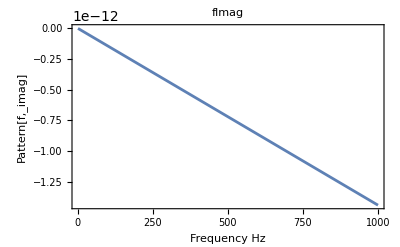

```mathematica
fIm=6/b^3((2χ)/ω)^(3/2)1/((Cos[ξd]Cosh[ξd])^2+(Sin[ξd]Sinh[ξd])^2)(Cos[ξd]Cosh[ξd](Sin[ξ]Cosh[ξ]+Cos[ξ]Sinh[ξ]-2 ξ Cos[ξ]Cosh[ξ] )-Sin[ξd]Sinh[ξd](-Sin[ξ]Cosh[ξ]+Cos[ξ]Sinh[ξ]+2 ξ Sin[ξ]Sinh[ξ]))/.
{ξ->b/2 √(ω/(2χ)),ξd->bd/2 √(ω/(2χ)),χ->λ/(ρ Cv)}/.
{ρ->7.93 10^3,Cv->460,λ->16.3,α->16.3 10^-8,ω->2π f,χ->4.47,b->2 10^-3,bd->3 10^-3};
Plot[fIm,{f,1,1000},PlotLabel->fImag, Frame->True,FrameLabel->{Frequency(Hz),f_imag}]
```